# Two-Qubit Gates

Section 2.2 of the Quantum Workbook (Springer, 2022)https://doi.org/10.1007/978-3-030-91214-7.

Properties of the CNOT gate

Usage examples of the CNOT gate

Controlled-unitary gates

Universality of the CNOT gate

Table of Contents

The CNOT Gate

Definition

Definition: Comprehension

Application: Copying basis states

References

Application: Entanglement creation

Application: Parity Measurement

References

Application: Addition of numbers

References

Variations

Controlled-Z Gate

What is it?

Relation to the CNOT gate?

SWAP Gate

Definition

Relation to the CNOT gate

Controlled-Unitary Gates

What is it?

Implementing it using the CNOT and Rotations

Universality of CNOT

Conclusion

Summary

Keywords

Functions

Related Links

## The CNOT Gate

### Definition

```mathematica
Let[Qubit,S]
```

```mathematica
cn=CNOT[S[1],S[2]]
```

CNOT[{S_1}→{1},{S_2}]

```mathematica
qc=QuantumCircuit[cn]
```

-Graphics-

```mathematica
op=Elaborate[qc];
op//PauliForm
```

(I⊗I)/2+(I⊗X)/2+(Z⊗I)/2-(Z⊗X)/2

```mathematica
Matrix[qc]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

```mathematica
in=Basis[S@{1,2}]
```

{0_S_10_S_2,0_S_11_S_2,1_S_10_S_2,1_S_11_S_2}

```mathematica
out=qc**in
```

{0_S_10_S_2,0_S_11_S_2,1_S_11_S_2,1_S_10_S_2}

```mathematica
Thread[in->out]//TableForm
```

0_S_10_S_2→0_S_10_S_2
0_S_11_S_2→0_S_11_S_2
1_S_10_S_2→1_S_11_S_2
1_S_11_S_2→1_S_10_S_2

### Definition: Comprehension

```mathematica
Let[Qubit,S]
```

```mathematica
Let[Binary,x]
```

```mathematica
qc=QuantumCircuit[
Ket[S@{1,2}->x@{1,2}],
CNOT[S[1],S[2]]]
```

-Graphics-

```mathematica
out=Elaborate[qc];
out//ProductForm
```

x_1⊗x_1⊕x_2

In summary,

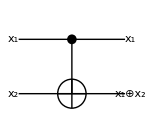

```mathematica
QuantumCircuit[
Ket[S@{1,2}->x@{1,2}],
CNOT[S[1],S[2]],
Ket[S[1]->x[1],S[2]->Mod[x[1]+x[2],2]],
"PortSize"->{0.7,1.4}
]
```

### Application: Copying basis states

Recall the defining property of the CNOT

-Graphics-

In particular,

In short, if the target qubit is initialized to 0, then the CNOT gate “copies” the basis state of the control qubit to the target.

```mathematica
qc=QuantumCircuit[CNOT[S[1],S[2]]]
```

-Graphics-

```mathematica
in=Basis[S@{1,2}];
out=qc**in;
Thread[in->out]//TableForm
```

0_S_10_S_2→0_S_10_S_2
0_S_11_S_2→0_S_11_S_2
1_S_10_S_2→1_S_11_S_2
1_S_11_S_2→1_S_10_S_2

Now, take a superposition state as input.

```mathematica
in=S[1,6]**Ket[]
```

(0_S_1)/(√2)+(1_S_1)/(√2)

```mathematica
out=qc**in
```

(0_S_10_S_2)/(√2)+(1_S_11_S_2)/(√2)

Question: The output state is not the copy of the input state. That is, for the output state, we expected

(0+1)/(√2)⊗(0+1)/(√2)=1/2(00+01+10+11)

What’s wrong?

No-cloning theorem: Quantum mechanics does not allow to copy an unknown state.

(0 c_0+1 c_1)⊗0↦(0 c_0+1 c_1)⊗(0 c_0+1 c_1) : NOT ALLOWED!

The previous copying-like feature was possible because the input state was one of the basis states.

#### References

Tutorial: “No-Cloning Theorem”

### Application: Entanglement creation

```mathematica
sp=QuantumCircuit[Ket[S@{1,2}],S[1,6]]
```

-Graphics-

```mathematica
out=Elaborate[sp]
```

(0_S_10_S_2)/(√2)+(1_S_10_S_2)/(√2)

```mathematica
KetFactor[out]
```

((0_S_1+1_S_1)⊗0_S_2)/(√2)

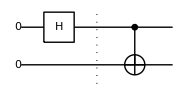

```mathematica
qc=QuantumCircuit[sp,"Separator",CNOT[S[1],S[2]]]
```

```mathematica
out=Elaborate[qc]
```

(0_S_10_S_2)/(√2)+(1_S_11_S_2)/(√2)

### Application: Parity Measurement

Recall, again, the defining property of the CNOT

-Graphics-

Recall: In a quantum computer,  parity values ±1 are expressed in binary digits 0 and 1:
		Piecewise[{{+1  →, 0}, {-1  →, 1}}]

```mathematica
in1=Tuples[{1,-1},3];
out1=Times@@@in1;
in2=Tuples[{0,1},3];
out2=Mod[Total@#,2]&@@@in2;
Row@{
TableForm[Thread[in1->out1]],"\t\t",
TableForm[Thread[in2->out2]]
}
```

{1,1,1}→1
{1,1,-1}→-1
{1,-1,1}→-1
{1,-1,-1}→1
{-1,1,1}→-1
{-1,1,-1}→1
{-1,-1,1}→1
{-1,-1,-1}→-1		{0,0,0}→0
{0,0,1}→0
{0,1,0}→0
{0,1,1}→0
{1,0,0}→1
{1,0,1}→1
{1,1,0}→1
{1,1,1}→1

```mathematica
Let[Qubit,S,T]
```

```mathematica
$n=4;
kk=Range[$n]
```

{1,2,3,4}

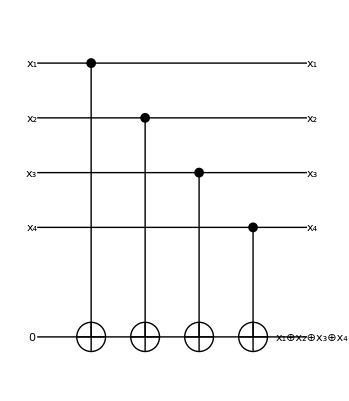

```mathematica
cc=Thread[Hold[CNOT][S[kk],T]]//ReleaseHold;
QuantumCircuit[
Ket[S[kk]->x[kk]],Ket[{T}],
Sequence@@cc,
Ket[S[kk]->x[kk]],
Ket[T->Mod[Total@x@kk,2]],
"Invisible"->S[$n+1/2],
"PortSize"->{0.7,4}
]
```

#### References

Tutorial: “Pauli Measurements”

Tutorial: “Quantum Error-Correction Codes”

### Application: Addition of numbers

Recall: A sequence of CNOT gates “adds up” the binary numbers.

-Graphics-

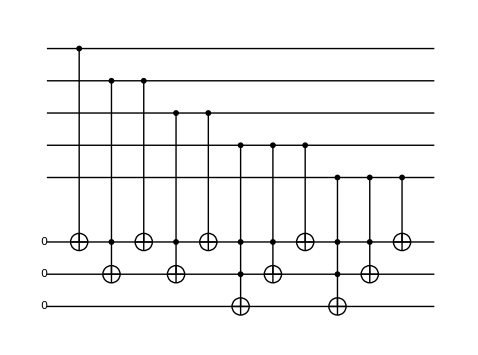

#### References

Tutorial: “Addition of Numbers”

Tutorial: “Measurement of Total Pauli Z”

Tutorial: “Entanglement Distillation”

### Variations

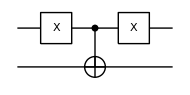

```mathematica
qc=QuantumCircuit[S[1,1],CNOT[S[1],S[2]],S[1,1]]
```

```mathematica
cnn=CNOT[S[1]->0,S[2]]
```

CNOT[{S_1}→{0},{S_2}]

```mathematica
new=QuantumCircuit[cnn]
```

-Graphics-

```mathematica
Elaborate[new]//PauliForm
```

(I⊗I)/2+(I⊗X)/2-(Z⊗I)/2+(Z⊗X)/2

```mathematica
Matrix[new]//MatrixForm
```

(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
in=Basis[S@{1,2}]
```

{0_S_10_S_2,0_S_11_S_2,1_S_10_S_2,1_S_11_S_2}

```mathematica
out=new**in
```

{0_S_11_S_2,0_S_10_S_2,1_S_10_S_2,1_S_11_S_2}

```mathematica
Thread[in->out]//TableForm
```

0_S_10_S_2→0_S_11_S_2
0_S_11_S_2→0_S_10_S_2
1_S_10_S_2→1_S_10_S_2
1_S_11_S_2→1_S_11_S_2

## Controlled-Z Gate

### What is it?

```mathematica
Let[Qubit,S]
```

```mathematica
cz=CZ[S[1],S[2]]
```

CZ[{S_1},{S_2}]

```mathematica
qc=QuantumCircuit[cz]
```

-Graphics-

```mathematica
Elaborate[cz]
```

1/2-1/2 S_1^zS_2^z+S_1^z/2+S_2^z/2

```mathematica
mat=Matrix[cz];
mat//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)

```mathematica
in=Basis[S@{1,2}]
```

{0_S_10_S_2,0_S_11_S_2,1_S_10_S_2,1_S_11_S_2}

```mathematica
out=cz**in
```

{0_S_10_S_2,0_S_11_S_2,1_S_10_S_2,-1_S_11_S_2}

```mathematica
Thread[in->out]//TableForm
```

0_S_10_S_2→0_S_10_S_2
0_S_11_S_2→0_S_11_S_2
1_S_10_S_2→1_S_10_S_2
1_S_11_S_2→-1_S_11_S_2

### Relation to the CNOT gate?

The CNOT and CZ gates are closely related to each other. To see it, recall that HXH=Z.

```mathematica
cn=QuantumCircuit[CNOT[S[1],S[2]]]
```

-Graphics-

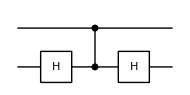

```mathematica
new=QuantumCircuit[S[2,6],CZ[S[1],S[2]],S[2,6]]
```

```mathematica
cn-new//Elaborate
```

0

Using the identity above and the fact that the CZ gate is symmetric about the control and target qubits, applying the Hadamard gates can reverse the roles of the control and target qubits for the CNOT gate.

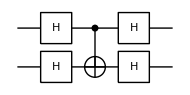

```mathematica
qc=QuantumCircuit[S[{1,2},6],CNOT[S[1],S[2]],S[{1,2},6]]
```

```mathematica
new=QuantumCircuit[CNOT[S[2],S[1]]]
```

-Graphics-

```mathematica
qc-new//Elaborate
```

0

## SWAP Gate

### Definition

```mathematica
Let[Qubit,S]
```

```mathematica
op=SWAP[S[1],S[2]]
```

SWAP[S_1,S_2]

```mathematica
Elaborate[op]
```

1/2+1/2 S_1^xS_2^x+1/2 S_1^yS_2^y+1/2 S_1^zS_2^z

The SWAP gate exchanges the states of the two qubits.

```mathematica
in=Basis[S@{1,2}];
out=op**in;
Thread[in->out]//TableForm
```

0_S_10_S_2→0_S_10_S_2
0_S_11_S_2→1_S_10_S_2
1_S_10_S_2→0_S_11_S_2
1_S_11_S_2→1_S_11_S_2

This is the matrix representation of the SWAP gate in the logical basis.

```mathematica
Matrix[op]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)

In the quantum circuit model, the SWAP gate is represented as follows.

```mathematica
qc=QuantumCircuit[SWAP[S[1],S[2]]]
```

-Graphics-

### Relation to the CNOT gate

The SWAP gate can be implemented by means of the CNOT gate.

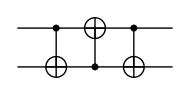

```mathematica
new=QuantumCircuit[CNOT[S[1],S[2]],CNOT[S[2],S[1]],CNOT[S[1],S[2]]]
```

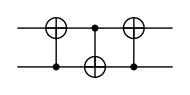

```mathematica
more=QuantumCircuit[CNOT[S[2],S[1]],CNOT[S[1],S[2]],CNOT[S[2],S[1]]]
```

```mathematica
Elaborate[qc-new]
Elaborate[qc-more]
```

0

0

## Controlled-Unitary Gates

### What is it?

### Implementing it using the CNOT and Rotations

## Universality of CNOT

What do you need to implement an arbitrary two-qubit gates?

For an arbitrary two-qubit unitary gate, the procedure is detailed  in “Two-Qubit Gates.”

### Conclusion

## Summary

### Keywords

CNOT gate, CZ gate

SWAP gate

Controlled-unitary gates

Universality of the CNOT gate

### Functions

CNOT, CX, CZ

SWAP

ControlledGate

### Related Links

Section 2.2 of the Quantum Workbook (2022, 2023).

Tutorial: “Two-Qubit Gates”